```mathematica
f[x_] = Sin[x]
```

Sin[x]

```mathematica
nodesA = {-1,-0.3,0.3,1}
```

{-1,-0.3,0.3,1}

```mathematica
derivative= D[f[x],{x,4}]
```

Sin[x]

```mathematica
maxD = MaxValue[{derivative,x≤1,x≥1},x]
```

Sin[1]

```mathematica
w[x_] = (x- nodesA[[1]])*(x- nodesA[[2]])*(x-nodesA[[3]])*(x-nodesA[[4]])
```

(-1+x) (-0.3+x) (0.3+x) (1+x)

```mathematica
errFunc[x_] = (Abs[maxD]*Abs[w[x]])/Factorial[4]
```

1/24 Abs[(-1+x) (-0.3+x) (0.3+x) (1+x)] Sin[1]

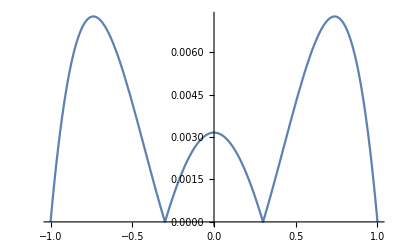

```mathematica
Plot[errFunc[x],{x,-1,1}]
```

```mathematica
chebyshev[k_] = Cos[((2k-1)*Pi)/(2*4)]
```

Cos[1/8 (-1+2 k) π]

```mathematica
nodesB = Table[chebyshev[i],{i,1,4}]
```

{Cos[π/8],Sin[π/8],-Sin[π/8],-Cos[π/8]}

```mathematica
wCheby[x_] = (x- nodesB[[1]])*(x- nodesB[[2]])*(x-nodesB[[3]])*(x-nodesB[[4]])
```

(x-Cos[π/8]) (x+Cos[π/8]) (x-Sin[π/8]) (x+Sin[π/8])

```mathematica
errChebyFunc[x_]= (Abs[maxD]*Abs[wCheby[x]])/Factorial[4]
```

1/24 Abs[(x-Cos[π/8]) (x+Cos[π/8]) (x-Sin[π/8]) (x+Sin[π/8])] Sin[1]

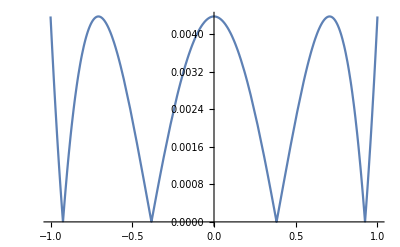

```mathematica
Plot[errChebyFunc[x],{x,-1,1}]
```